## 3^rd Order ΔΣM Block Diagram Reduction

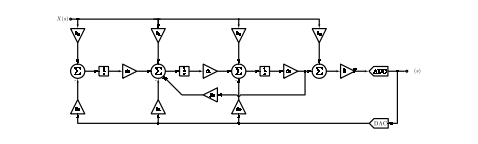

## Equations

#### Gains:

```mathematica
Subscript[P, 1]=(Subscript[b, 0] Subscript[c, 0] Subscript[c, 1] Subscript[c, 2] k)/s^3;
Subscript[P, 2]=(Subscript[b, 1] Subscript[c, 1] Subscript[c, 2] k)/s^2;
Subscript[P, 3]=(Subscript[b, 2] Subscript[c, 2] k)/s;
Subscript[P, 4]=Subscript[b, 3] k;
```

#### Loops:

```mathematica
Subscript[L, 1]=(-Subscript[a, 0] Subscript[c, 0] Subscript[c, 1] Subscript[c, 2] k)/s^3;
Subscript[L, 2]=(-Subscript[a, 1] Subscript[c, 1] Subscript[c, 2] k)/s^2;
Subscript[L, 3]=(-Subscript[a, 2] Subscript[c, 2] k)/s;
Subscript[L, 4]=(-Subscript[g, 0] Subscript[c, 1] Subscript[c, 2])/s^2;
```

#### Δ_i's

```mathematica
Subscript[Δ, 1]=1;
Subscript[Δ, 2]=1;
Subscript[Δ, 3]=1;
Subscript[Δ, 4]=1-Subscript[L, 4];
```

#### System Δ

```mathematica
Subscript[D, s]=1-(Subscript[L, 1]+Subscript[L, 2]+Subscript[L, 3]+Subscript[L, 4]);
```

## Transfer Functions

#### Signal Transfer Function

```mathematica
STF=(Subscript[P, 1] Subscript[Δ, 1]+Subscript[P, 2] Subscript[Δ, 2]+Subscript[P, 3] Subscript[Δ, 3]+Subscript[P, 4] Subscript[Δ, 4])/Subscript[D, s]//Cancel;
STF=STF/.{k->1,Subscript[c, 0]->1,Subscript[c, 1]->1,Subscript[c, 2]->1}
```

(b_0+s b_1+s^2 b_2+s^3 b_3+s b_3 g_0)/(s^3+a_0+s a_1+s^2 a_2+s g_0)

#### Noise Transfer Function

```mathematica
Subscript[P, 5]=1; Subscript[Δ, 5]=1-Subscript[L, 4]; (* Unity Gain Forwad Path *)
```

```mathematica
NTF=(Subscript[P, 5] Subscript[Δ, 5])/Subscript[D, s]//Cancel;
```

```mathematica
NTF=NTF/.{k->1,Subscript[c, 0]->1,Subscript[c, 1]->1,Subscript[c, 2]->1}
```

(s (s^2+g_0))/(s^3+a_0+s a_1+s^2 a_2+s g_0)

## Solution

```mathematica
STFnum = CoefficientList[Numerator[STF],s];
Den = CoefficientList[Denominator[STF],s];
NTFnum = CoefficientList[Numerator[NTF],s];
```

```mathematica
FCoeff={Subscript[F, 4],Subscript[F, 3],Subscript[F, 2],Subscript[F, 1]};
MCoeff={Subscript[M, 4],Subscript[M, 3],Subscript[M, 2],Subscript[M, 1]};
GCoeff={Subscript[G, 4],Subscript[G, 3],Subscript[G, 2],Subscript[G, 1]};

Solve[
{
FCoeff[[1]]==STFnum[[1]],
FCoeff[[2]]==STFnum[[2]],
FCoeff[[3]]==STFnum[[3]],
FCoeff[[4]]==STFnum[[4]],
MCoeff[[1]]==Den[[1]],
MCoeff[[2]]==Den[[2]],
MCoeff[[3]]==Den[[3]],
MCoeff[[4]]==Den[[4]],
GCoeff[[1]]==NTFnum[[1]],
GCoeff[[2]]==NTFnum[[2]],
GCoeff[[3]]==NTFnum[[3]],
GCoeff[[4]]==NTFnum[[4]]
},
{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[b, 0],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}
]//Transpose//TableForm
```

a_0→M_4
a_1→-g_0+M_3
a_2→M_2
b_0→F_4
b_1→F_3-F_1 g_0
b_2→F_2
b_3→F_1